```mathematica
PDE = D[V[x,y], x, x] + D[V[x,y], y, y];
```

```mathematica
BCs = {DirichletCondition[V[x,y] == 0.1, y==0],
DirichletCondition[V[x,y] ==0.1, y==1],
DirichletCondition[V[x,y]==0.1, x==0],
DirichletCondition[V[x,y]==0.1, x==1]};
```

```mathematica
ufun = NDSolveValue[{PDE == 0, BCs}, V, {x, 0, 1}, {y, 0, 1}];
```

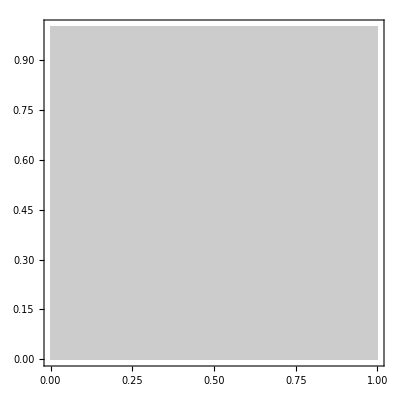

```mathematica
ContourPlot[ufun[x,y], {x, 0, 1}, {y, 0, 1}]
```

```mathematica
f[x,y] = (x^2 + y^2)*Sin[x*y]
```

(x^2+y^2) Sin[x y]

```mathematica
ufun = NDSolve[{PDE == f[x,y], BCs}, V, {x, 0, 1}, {y, 0, 1}];
```

```mathematica
ContourPlot[ufun[x,y], {x, 0, 1}, {y, 0, 1}]
```

-Graphics-

```mathematica
ufun
```

{{V→InterpolatingFunction[…]}}